```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,xcolor,bm,mhchem}","\\definecolor{darkgreen}{RGB}{0, 180, 0}"}];
```

```mathematica
HUMP[λ_,t_,U_]=({{-(2 t^2 λ)/U, 0, 0, (2 t^2 λ)/U}, {0, U-(2 t^2 λ)/U, (2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U}, {0, (2 t^2 λ)/U, U-(2 t^2 λ)/U, -(2 t √(-4 t^2+U^2) λ)/U}, {(2 t^2 λ)/U, (2 t √(-4 t^2+U^2) λ)/U, -(2 t √(-4 t^2+U^2) λ)/U, -2 U (-1+λ)+(6 t^2 λ)/U}});
HRMP[λ_,t_,U_]=({{-2 t+U-(U λ)/2, 0, 0, (U λ)/2}, {0, U-(U λ)/2, (U λ)/2, 0}, {0, (U λ)/2, U-(U λ)/2, 0}, {(U λ)/2, 0, 0, 2 t+U-(U λ)/2}});
```

```mathematica
Solve[
{
Det[HRMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]],D[Det[HRMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]], Ε]
}==0,{Ε,λ}]
```

{{Ε→ⅈ (2 t-ⅈ U),λ→-(4 ⅈ t)/U},{Ε→-ⅈ (2 t+ⅈ U),λ→(4 ⅈ t)/U},{Ε→U,λ→0}}

```mathematica
Abs[-(4 ⅈ t)/U]
```

4 Abs[t/U]

```mathematica
RadConv[t_,U_]:=
Sort[
Abs[λ]/.NSolve[
{
Det[HUMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]],D[Det[HUMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]], Ε]
}==0,{Ε,λ}]
]//DeleteDuplicates
```

```mathematica
TabRadConv=With[{ΔU=1/100},Table[{U,RadConv[1,U]},{U,2+ΔU,10,ΔU}]];
```

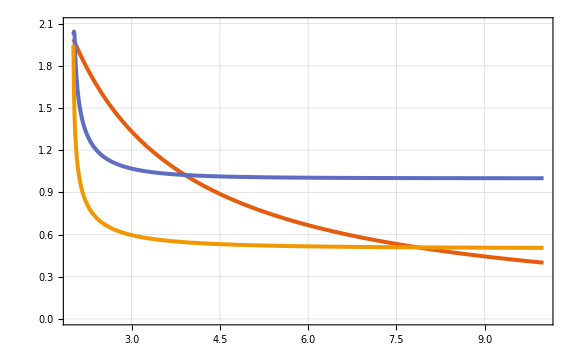

```mathematica
ListPlot[{
Table[{TabRadConv⟦k,1⟧,4/TabRadConv⟦k,1⟧},{k,Length[TabRadConv]}],
Table[{TabRadConv⟦k,1⟧,TabRadConv⟦k,2,3⟧},{k,Length[TabRadConv]}],
Table[{TabRadConv⟦k,1⟧,TabRadConv⟦k,2,2⟧},{k,Length[TabRadConv]}]
},Joined->True,InterpolationOrder->1,PlotTheme->"Scientific",
PlotRange->{{2,10},{0,2.1}},PlotStyle->Thickness[0.005],
BaseStyle->20,ImageSize->Large,GridLines->Automatic,FrameLabel->{MaTeX["U/t",FontSize->20],MaTeX["\\text{Radius of convergence } r_c",FontSize->20]},
PlotLegends->Placed[{MaTeX["r_c \\text{ for RMP ground state}",FontSize->20],MaTeX["r_c \\text{ for UMP ground state}",FontSize->20],MaTeX["r_c \\text{ for UMP excited state}",FontSize->20]},{Right,Top}]]
```

```mathematica
RadConv[t_,U_]:=
Sort[
Abs[λ]/.NSolve[
{
Series[Det[HUMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]],{U,∞,0}]//Normal,
D[Det[HUMP[λ,t,U]-Ε IdentityMatrix[Length[HUMP[λ,t,U]]]], Ε]
},{Ε,λ}]
]//DeleteDuplicates
```